{plot2Doption,plot3Doption,framelabel[xlabel_String,ylabel_String,size_:20],axeslabel2D[xlabel_String,ylabel_String,size_:20],axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20],axeslabel[labels_List,size_: 20],importData,jsonInfo,interpolateAndFourier[time_List,disp_List,timeSpan_List: {}],interpolateAndFourierTr[timedisp_List,timeSpan_List: {}],MyFourier[list_,n_],MyInverseFourier[list_,n_],MyDiscreteConvolve[f_,g_],MyDiscreteConvolveUsingCn[FourierGF_],Rv[q_],Rs[q_],W2dQdt[q_,w_],Q2Roll[{a_,b_,c_,d_}],Q2Pitch[{a_,b_,c_,d_}],Q2Yaw[{a_,b_,c_,d_}],getOmegaFromKandDepth[k_,h_],getOmegaFromLandDepth[L_,h_],getTFromLandDepth[L_,h_],getkFromTandDepth[T_,h_]}

1.93625

6.45578

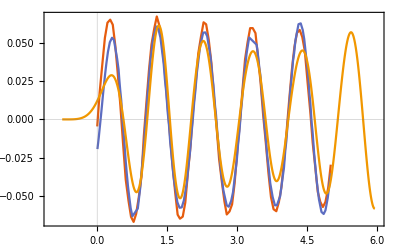

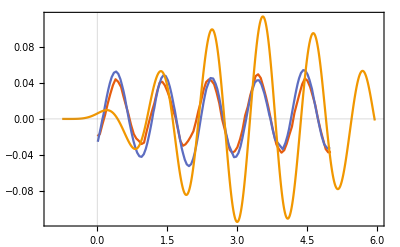

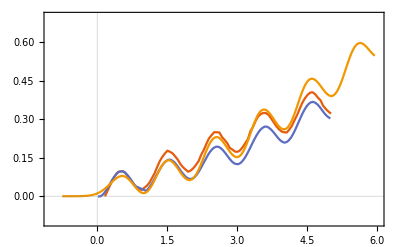

```mathematica
Clear["Global`*"]
NotebookEvaluate["~/Dropbox/code/mathematica_plot_options.nb"]
filename="/Users/tomoaki/BEM/Ren2015_2D_H0d04_T1d2_DT0d05_ELEMlinear_ALEpseudo_quad_ALEPERIOD1/result.json";
jsonInfo[filename];
data=Import[filename];

d=0.4;
T=1.2;
k=getkFromTandDepth[T,d];
L=2π/k
c=L*T;
15/c
shift=0.75;

dir = "/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Ren2015/";
dataHeave=Import[FileNameJoin[{dir,"Ren2015_Fig11_H0d04_T1d2_heave.csv"}]];
dataHeaveSPH=Import[FileNameJoin[{dir,"Ren2015_Fig11_H0d04_T1d2_heave_SPH.csv"}]];
dataPitchSPH=Import[FileNameJoin[{dir,"Ren2015_Fig11_H0d04_T1d2_pitch_SPH.csv"}]];
dataSurgeSPH=Import[FileNameJoin[{dir,"Ren2015_Fig11_H0d04_T1d2_surge_SPH.csv"}]];
maxt=6;
ListPlot[{
{#1,#2}&@@@dataHeave,
{#1,#2}&@@@dataHeaveSPH,Transpose[{("simulation_time"/.data)/T-shift,(("float_COM"/.data)[[;;,3]]-0.4)/d}]}
,Joined->{True,True,True}
,PlotRange->{{-1,maxt},All}
,(*PlotMarkers->Automatic,*)Evaluate[plot2Doption]]
dataPitch=Import[FileNameJoin[{dir,"Ren2015_Fig11_H0d04_T1d2_pitch.csv"}]];
ListPlot[{
{#1,#2}&@@@dataPitch
,{#1,#2}&@@@dataPitchSPH
,Transpose[{("simulation_time"/.data)/T-shift,("float_pitch"/.data)/(d*k)}]}
,Joined->True
,PlotRange->{{-1,maxt},All}
,(*PlotMarkers->Automatic,*)Evaluate[plot2Doption]]
dataSurge=Import[FileNameJoin[{dir,"Ren2015_Fig11_H0d04_T1d2_surge.csv"}]];
ListPlot[{
{#1,#2-0.02}&@@@dataSurge
,{#1,#2-0.025}&@@@dataSurgeSPH
,Transpose[{("simulation_time"/.data)/T-shift,("float_COM"/.data)[[;;,1]]/d}]}
,Joined->True
,PlotRange->{{-1,maxt},{-0.1,0.7}}
,(*PlotMarkers->Automatic,*)Evaluate[plot2Doption]]
```

```mathematica
(*Manipulate[
heaveExp=Interpolation[{T*#1,d*#2}&@@@dataHeave];
heaveSimu=Interpolation[Transpose[{("simulation_time"/.data)-shift,("float_COM"/.data)[[;;,3]]-0.4}]];
ListPlot[Table[{t,heaveSimu[t]-heaveExp[t]},{t,0.01,4,0.1}],Joined->True];

pitchExp=Interpolation[{T*#1,d*k*#2}&@@@dataPitch];
pitchSimu=Interpolation[Transpose[{("simulation_time"/.data)-shift,("float_pitch"/.data)}]];
ListPlot[Table[{t,(heaveSimu[t]-heaveExp[t])+a*(pitchSimu[t]-pitchExp[t])},{t,0.01,4,0.1}]
,Joined->True
,PlotLabel->{a,shift}
,PlotRange->{All,{-0.01,0.01}}]
,{a,-1,1,0.0001}
,{shift,0.9,2.5,0.01}]*)
```

{plot2Doption,plot3Doption,framelabel[xlabel_String,ylabel_String,size_:20],axeslabel2D[xlabel_String,ylabel_String,size_:20],axeslabel3D[xlabel_String,ylabel_String,zlabel_String,size_:20],axeslabel[labels_List,size_: 20],importData,jsonInfo,interpolateAndFourier[time_List,disp_List,timeSpan_List: {}],interpolateAndFourierTr[timedisp_List,timeSpan_List: {}],MyFourier[list_,n_],MyInverseFourier[list_,n_],MyDiscreteConvolve[f_,g_],MyDiscreteConvolveUsingCn[FourierGF_],Rv[q_],Rs[q_],W2dQdt[q_,w_],Q2Roll[{a_,b_,c_,d_}],Q2Pitch[{a_,b_,c_,d_}],Q2Yaw[{a_,b_,c_,d_}],getOmegaFromKandDepth[k_,h_],getOmegaFromLandDepth[L_,h_],getTFromLandDepth[L_,h_],getkFromTandDepth[T_,h_]}

1.93625

6.45578

{/Users/tomoaki/BEM/benchmark20250117_Fredriksen2015/Fredriksen2015_WS0d01667_T0d6_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json,/Users/tomoaki/BEM/benchmark20250117_Fredriksen2015/Fredriksen2015_WS0d01667_T0d65_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json,/Users/tomoaki/BEM/benchmark20250117_Fredriksen2015/Fredriksen2015_WS0d01667_T0d7_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json,/Users/tomoaki/BEM/benchmark20250117_Fredriksen2015/Fredriksen2015_WS0d01667_T0d9_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json,/Users/tomoaki/BEM/benchmark20250117_Fredriksen2015/Fredriksen2015_WS0d01667_T0d95_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json,/Users/tomoaki/BEM/benchmark20250117_Fredriksen2015/Fredriksen2015_WS0d01667_T1d_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json}

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/benchmark20250117_Fredriksen2015/Fredriksen2015_WS0d01667_T1d_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

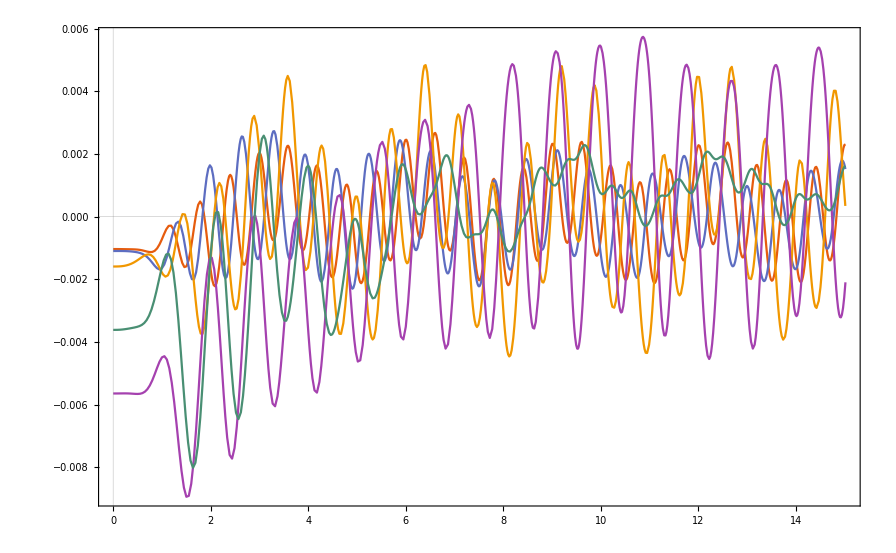

Power::infy: 無限式1/0.が見付かりました．

General::stop: この計算中に，Power::infyのこれ以上の出力は表示されません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/benchmark20250117_Fredriksen2015/Fredriksen2015_WS0d01667_T1d_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

-Graphics3D-

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/benchmark20250117_Fredriksen2015/Fredriksen2015_WS0d01667_T1d_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

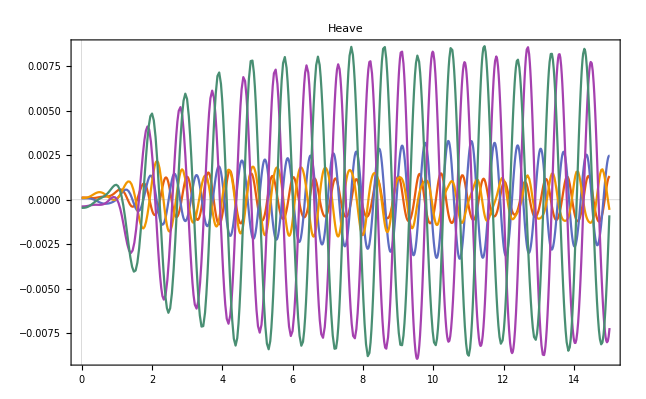

Power::infy: 無限式1/0.が見付かりました．

General::stop: この計算中に，Power::infyのこれ以上の出力は表示されません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/benchmark20250117_Fredriksen2015/Fredriksen2015_WS0d01667_T1d_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

ListPlot::lpn: {{{ComplexInfinity,0.0000997156},{15.0157,0.0000693099},{7.50785,0.0000403954},{5.00523,0.0000367339},{3.75392,0.0000271436},{3.00314,0.0000260692},{2.50262,0.0000214527},{2.1451,0.0000233603},{1.87696,0.0000171342},{1.66841,0.0000131572},«338»},«4»,{}}は数値のリストあるいは数値の対のリストではありません．

Power::infy: 無限式1/0.が見付かりました．

General::stop: この計算中に，Power::infyのこれ以上の出力は表示されません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/benchmark20250117_Fredriksen2015/Fredriksen2015_WS0d01667_T1d_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

-Graphics3D-

Power::infy: 無限式1/0.が見付かりました．

General::stop: この計算中に，Power::infyのこれ以上の出力は表示されません．

Import::nffil: Importの最中にファイル/Users/tomoaki/BEM/benchmark20250117_Fredriksen2015/Fredriksen2015_WS0d01667_T1d_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.jsonが見付かりませんでした．

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

General::stop: この計算中に，ReplaceAll::repsのこれ以上の出力は表示されません．

-Graphics3D-

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,3⟧の長さはオブジェクトの深さを超えています．

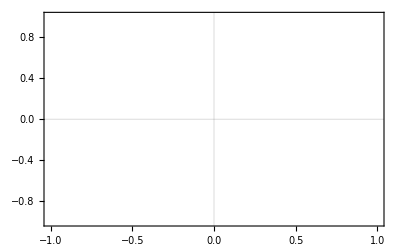

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

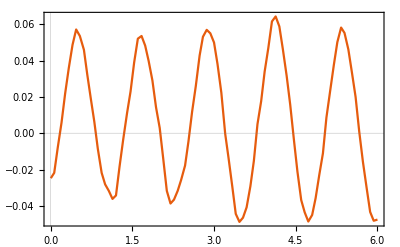

ReplaceAll::reps: {$Failed}は置換規則のリストでも有効なディスパッチ表でもないため，置換には使用できません．

Part::partd: 部分指定(float_COM/.$Failed)⟦1;;All,1⟧の長さはオブジェクトの深さを超えています．

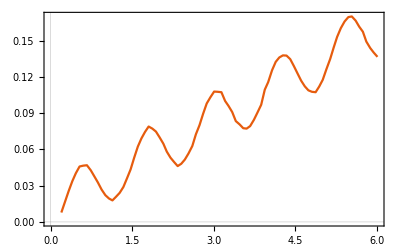

```mathematica
Clear["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../../mathematica_plot_options.nb"}]]

d=0.4;
T=1.2;
k=getkFromTandDepth[T,d];
L=2π/k
c=L*T;
15/c
shift=0.9;

Ts={0.6,0.65,0.7,0.9,0.95,1.0};
filenames=Table["/Users/tomoaki/BEM/benchmark20250117_Fredriksen2015/Fredriksen2015_WS0d01667_T"<>StringReplace[ToString[i],"."->"d"]<>"_DT0d05_ELEMpseudo_quad_ALEpseudo_quad_ALEPERIOD1/result.json",{i,Ts}]

start=1;

DATA=Table[data=Import[name];Transpose[{("simulation_time"/.data)[[start;;]],("float_COM"/.data)[[start;;,1]]-Mean[("float_COM"/.data)[[start;;,1]]]}],{name,filenames}];
ListPlot[DATA,Evaluate[plot2Doption]]

DATA=Table[data=Import[filenames[[i]]];{Ts[[i]],If[1/#1==ComplexInfinity,0,1/#1],#2}&@@@interpolateAndFourier[("simulation_time"/.data)[[start;;]],("float_COM"/.data)[[start;;,1]]-Mean[("float_COM"/.data)[[start;;,1]]]],{i,1,Length[filenames],1}];
ListLinePlot3D[DATA,PlotRange->All,PlotLegends->filenames]

DATA=Table[data=Import[name];Transpose[{("simulation_time"/.data)[[start;;]],("float_COM"/.data)[[start;;,3]]-Mean[("float_COM"/.data)[[start;;,3]]]}],{name,filenames}];
ListPlot[DATA,Evaluate[plot2Doption]
,PlotLabel->"Heave"]

DATA=Table[data=Import[name];{1/#1,#2}&@@@interpolateAndFourier[("simulation_time"/.data)[[start;;]],("float_COM"/.data)[[start;;,3]]-Mean[("float_COM"/.data)[[start;;,3]]]],{name,filenames}];
ListPlot[DATA,PlotRange->{{0,3},All}
,PlotRange->All,Evaluate[plot2Doption]
,PlotLegends->filenames
,PlotLabel->"Heave"]

DATA=Table[data=Import[filenames[[i]]];{Ts[[i]],If[1/#1==ComplexInfinity,0,1/#1],#2}&@@@interpolateAndFourier[("simulation_time"/.data)[[start;;]],("float_COM"/.data)[[start;;,3]]-Mean[("float_COM"/.data)[[start;;,3]]]],{i,1,Length[filenames],1}];
ListLinePlot3D[DATA
,PlotRange->All
,PlotLegends->filenames
,PlotLabel->"Heave"]


DATA=Table[data=Import[filenames[[i]]];{Ts[[i]],If[1/#1==ComplexInfinity,0,1/#1],#2}&@@@interpolateAndFourier[("simulation_time"/.data)[[start;;]],("float_pitch"/.data)[[start;;]]-Mean[("float_pitch"/.data)[[start;;]]]],{i,1,Length[filenames],1}];
ListLinePlot3D[DATA
,PlotRange->All
,PlotLegends->filenames
,PlotLabel->"Pitch"]

dataHeave=Import[FileNameJoin[{NotebookDirectory[],"Ren2015_Fig11_H0d04_T1d2_heave.csv"}]];
ListPlot[{(*{T*#1,d*#2}&@@@dataHeave,*)Transpose[{("simulation_time"/.data)-shift,("float_COM"/.data)[[;;,3]]-(1-0.097+0.091)}]},Joined->True,(*PlotMarkers->Automatic,*)Evaluate[plot2Doption]]
dataPitch=Import[FileNameJoin[{NotebookDirectory[],"Ren2015_Fig11_H0d04_T1d2_pitch.csv"}]];
ListPlot[{{T*#1,d*k*#2}&@@@dataPitch,Transpose[{("simulation_time"/.data)-shift,("float_pitch"/.data)}]},Joined->True,(*PlotMarkers->Automatic,*)Evaluate[plot2Doption]]
dataSurge=Import[FileNameJoin[{NotebookDirectory[],"Ren2015_Fig11_H0d04_T1d2_surge.csv"}]];
ListPlot[{{T*#1,d*#2}&@@@dataSurge,Transpose[{("simulation_time"/.data)-shift,0.04+("float_COM"/.data)[[;;,1]]}]},Joined->True,(*PlotMarkers->Automatic,*)Evaluate[plot2Doption]]
```

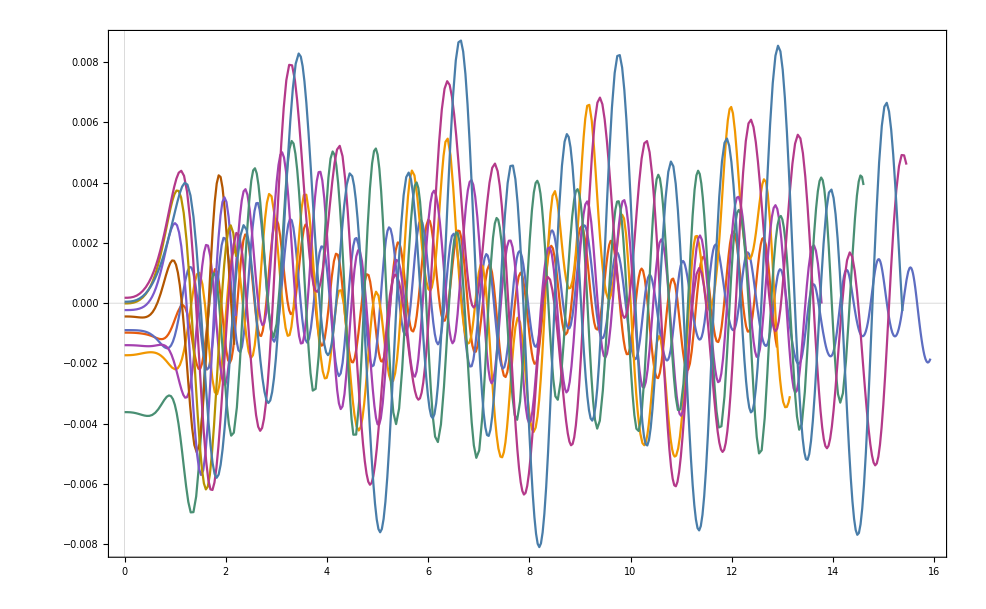

Power::infy: 無限式1/0.が見付かりました．

General::stop: この計算中に，Power::infyのこれ以上の出力は表示されません．

-Graphics3D-

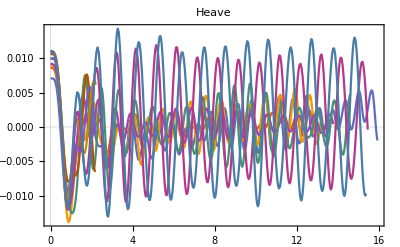

Power::infy: 無限式1/0.が見付かりました．

General::stop: この計算中に，Power::infyのこれ以上の出力は表示されません．

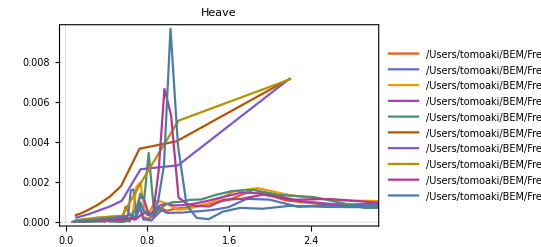

Power::infy: 無限式1/0.が見付かりました．

General::stop: この計算中に，Power::infyのこれ以上の出力は表示されません．

-Graphics3D-

Power::infy: 無限式1/0.が見付かりました．

General::stop: この計算中に，Power::infyのこれ以上の出力は表示されません．

-Graphics3D-